# xCellerator Example

ring-oscillator-michaelis-damped.nb

## A ring oscillator based on single-stage michaelis-menten reactions

Created: 02 August 2005 BES
Revised: 15 October 2007 (BES) to work with Mathematica version 6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:56:40.757009 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

## Damped oscillator

```mathematica
reactions={{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Z⟺ZP, X, XP],MM[K,v,K,v]}};odes=interpret[reactions];
r=run[odes, timeSpan-> 100,initialConditions-> {X-> 1, Z-> 1}, rates-> {v-> .5, K-> 0.01}];
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {XP,ZP}

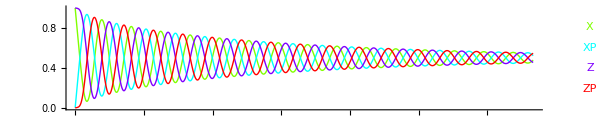

```mathematica
runPlot[r,PlotRange-> All, ImageSize-> 600, PlotPoints-> 100, AspectRatio-> .2]
```

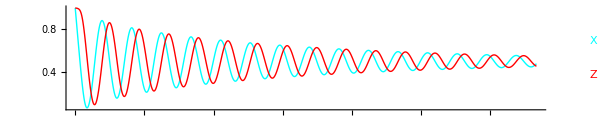

```mathematica
runPlot[r,{X,Z},PlotRange-> All, ImageSize-> 600, PlotPoints-> 100, AspectRatio-> .2]
```

## Limit as K->0: undamped: but variables can go negative!!

```mathematica
reactions={{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Z⟺ZP, X, XP],MM[K,v,K,v]}};odes=interpret[reactions];
r=run[odes, timeSpan-> 100,initialConditions-> {X-> 1, Z-> 1, ZP-> 1.1, XP-> 1.2}, rates-> {v-> .1, K-> 0}];
```

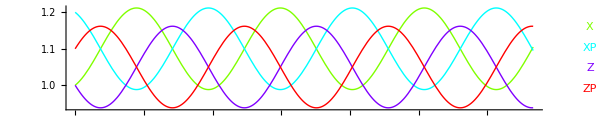

```mathematica
runPlot[r,PlotRange-> All, ImageSize-> 600, PlotPoints-> 100, AspectRatio-> .2]
```

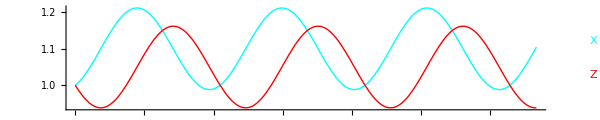

```mathematica
runPlot[r,{X,Z},PlotRange-> All, ImageSize-> 600, PlotPoints-> 100, AspectRatio-> .2]
```

## Limit is a simple harmonic oscillator

```mathematica
interpret[reactions/.{K-> 0}]
```

{{X'[t]==-v Z[t]+v ZP[t],XP'[t]==v Z[t]-v ZP[t],Z'[t]==v X[t]-v XP[t],ZP'[t]==-v X[t]+v XP[t]},{X,XP,Z,ZP}}

```mathematica
DSolve[{X'[t]==-v Z[t]+v ZP[t],XP'[t]==v Z[t]-v ZP[t],Z'[t]==v X[t]-v XP[t],ZP'[t]==-v X[t]+v XP[t], X[0]==X0,Z[0]==Z0, ZP[0]==ZP0, XP[0]==XP0},{X[t],XP[t],Z[t],ZP[t]}, {t}]
```

{{X[t]→1/2 (X0+XP0+X0 Cos[2 t v]-XP0 Cos[2 t v]-Z0 Sin[2 t v]+ZP0 Sin[2 t v]),XP[t]→1/2 (X0+XP0-X0 Cos[2 t v]+XP0 Cos[2 t v]+Z0 Sin[2 t v]-ZP0 Sin[2 t v]),Z[t]→1/2 (Z0+ZP0+Z0 Cos[2 t v]-ZP0 Cos[2 t v]+X0 Sin[2 t v]-XP0 Sin[2 t v]),ZP[t]→1/2 (Z0+ZP0-Z0 Cos[2 t v]+ZP0 Cos[2 t v]-X0 Sin[2 t v]+XP0 Sin[2 t v])}}